```mathematica
D[(π (κ - 1/2) vth^2)^(-1/2)Gamma[κ+1]/Gamma[κ+1/2](1+v^2/((κ-1/2)vth^2))^(-(κ+1)), v]
```

```mathematica
dispersion[ω_, vth_, k_,κ_]:= ω(1  + I* Sqrt[Pi]*ω^3/k^3* (-1-κ)/(vth^3(-1/2+κ)^(3/2))*Gamma[κ+1]/Gamma[κ+1/2]*(1+(ω^2/(k^2 vth^2)+ 1.5)/(κ-1/2))^(-2-κ))

 damping[ω_, vth_, k_,κ_]:= ω*Sqrt[Pi]*ω^3/k^3* (-1-κ)/(vth^3(-1/2+κ)^(3/2))*Gamma[κ+1]/Gamma[κ+1/2]*(1+(ω^2/(k^2 vth^2)+ 1.5)/(κ-1/2))^(-2-κ)
```

Null^2

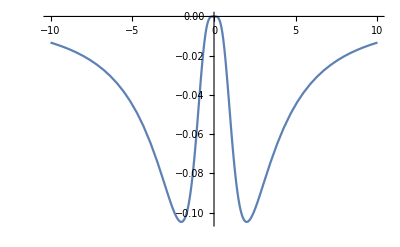

-Graphics-

```mathematica
Plot[damping[ω, 1, 1,1], {ω,-10,10}, PlotRange->All]
Plot[dispersion[ω, 1, 1,1], {ω,-10,10}, PlotRange->All]
```

(2 v (1+v^2/(vth^2 (-1/2+κ)))^(-2-κ) (-1-κ) Gamma[1+κ] -Graphics-)/(Null^2 √π vth^2 (-1/2+κ) √(vth^2 (-1/2+κ)) Gamma[1/2+κ])

-Graphics-

-Graphics-

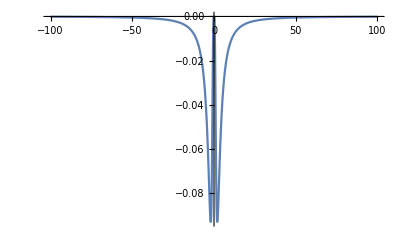

```mathematica
dispersionng[ω_, vth_, k_,κ]:= ω(1  + I* Sqrt[Pi]*ω^3/k^3* (-1-κ)/(vth^3(-1/2+κ)^(3/2))*(1+(ω^2/(k^2 vth^2)+ 1.5)/(κ-1/2))^(-2-κ))


Plot[dispersionng[ω, 1, 1,1], {ω,-100,100}, PlotRange->All]


dampingng[ω, vth, k,κ]:= ω*Sqrt[Pi]*ω^3/k^3* (-1-κ)/(vth^3(-1/2+κ)^(3/2))*(1+(ω^2/(k^2 vth^2)+ 1.5)/(κ-1/2))^(-2-κ)



Plot[dampingng[ω, 1, 1,1], {ω,-100,100}, PlotRange->All]
```